Loading the package

```mathematica
Needs["NDSolve`FEM`"]
```

Defining the system of equation

```mathematica
Clear[u,v,x,y]
op={({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

Defining the geometric region

RegionDifference[Rectangle[{0,0},{5,2}],Disk[{2.5,1},0.5]]

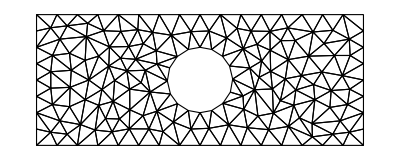

```mathematica
a=1.0;
reg1=Rectangle[{0,0},{5,2}];
reg2=Disk[{2.5,1},0.5];
Ω=RegionDifference[reg1,reg2]
mesh=ToElementMesh[Ω,"MaxCellMeasure"->0.05,"MeshOrder"->2,"MeshElementType"->TriangleElement];
mesh["Wireframe"]
```

Defining boundary conditions

```mathematica
Subscript[Γ, Du]=DirichletCondition[u[x,y]==0,x==0];
Subscript[Γ, Dv]=DirichletCondition[v[x,y]==0,x==0];
Subscript[Γ, Nv]=NeumannValue[-1,x==5];
```

Replacing the Young modulus and Poisson ratio in system of equations

```mathematica
op1=op/.{Y->10^3,ν->33/100};
```

Computations

```mathematica
{state}=NDSolve`ProcessEquations[{op1=={0,Subscript[Γ, Nv]},Subscript[Γ, Du],Subscript[Γ, Dv]},{u,v},{x,y}∈mesh]
femdata=state["FiniteElementData"];
pded=femdata["PDECoefficientData"];
bcd=femdata["BoundaryConditionData"];
md=femdata["FEMMethodData"];
sd=state["SolutionData"][[1]];
vd=state["VariableData"];
discretePDE=DiscretizePDE[pded,md,sd]
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];
discreteBCs=DiscretizeBoundaryConditions[bcd,md,sd]
ele=DiscretizePDE[pded,md,sd,"SaveFiniteElements"->True]
{stiffnessElements,nonzeroPos}=ele["StiffnessElements"];
```

{NDSolve`StateData[<SteadyState>]}

DiscretizedPDEData[<1256>]

DiscretizedBoundaryConditionData[<1256>]

DiscretizedPDEData[<1256>]

Defining the densities and modified stifness matrix

```mathematica
density=Table[ρ[i],{i,1,Length@stiffnessElements}];
modifiedElements=density*stiffnessElements;
```

Assemble

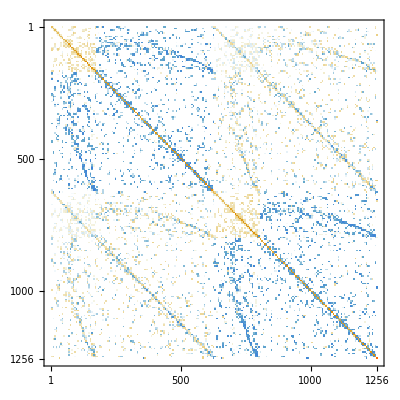
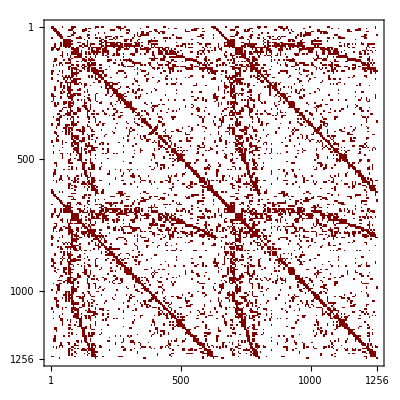

```mathematica
dof=md["DegreesOfFreedom"];
inci=Join@@md["Incidents"];
modifiedstiffness=AssembleMatrix[{inci,inci},modifiedElements,{dof,dof},"Sparse"->nonzeroPos];
{MatrixPlot[stiffness],MatrixPlot[modifiedstiffness]}
```

Defining the unknown displacements and extracting the coords of elements from mesh

```mathematica
displacement=Table[δ[i],{i,1,Length[stiffness]}];
coords=mesh["Coordinates"];
elems=mesh["MeshElements"];
```

Deploying boundary conditions on initial matrix and modified

```mathematica
DeployBoundaryConditions[{load,stiffness},discreteBCs]
DeployBoundaryConditions[{load,modifiedstiffness},discreteBCs]
```

DeployedBoundaryConditionData[<Insert>]

DeployedBoundaryConditionData[<Insert>]

Flattening the load vector for goal function

```mathematica
loadF=Flatten[load];
```

Defining the “area” of finite elements

```mathematica
square=Apply[0.5*((coords[[#3,1]]-coords[[#1,1]])*(coords[[#3,2]]+coords[[#1,2]])-(coords[[#2,1]]-coords[[#1,1]])*(coords[[#2,2]]+coords[[#1,2]])-(coords[[#3,1]]-coords[[#2,1]])*(coords[[#3,2]]+coords[[#2,2]]))&]/@elems[[1,1,1;;Length[stiffnessElements],1;;3]];
```

Defining the “Main” equations for “FindMinimum”

```mathematica
goalFunction=displacement.modifiedstiffness.displacement;
massEquation=∑_(k=1)^Length[square] square⟦k⟧ density⟦k⟧≤(∑_(k=1)^Length[square] square⟦k⟧) 1;
densityEq=Thread[(0.0≤#1≤1.5&)[density]];
equation=Table[modifiedstiffness⟦i⟧.displacement==loadF⟦i⟧,{i,1,Length[displacement]}];
```

Defining the system of equations and variables

```mathematica
sysOfEq=Flatten[{goalFunction,massEquation,equation,densityEq}];
sysOfEq//Length
variables=Flatten[{density,displacement}];
variables//Length
```

1540

1538

Defining the initial conditions

```mathematica
initDis=Thread[{#,0}&[displacement]];
initDen=Thread[{#,0.5}&[density]];
initCond=Flatten[{initDen,initDis},1];
```

Finding the minimum of “Goal function”

```mathematica
resultFMin=Quiet[FindMinimum[sysOfEq,initCond]];//AbsoluteTiming
minimizedDen=density/.resultFMin[[2]];
normModified=Normal[modifiedstiffness];
minimizedstiffness=normModified/.resultFMin[[2]];
```

{26.133,Null}

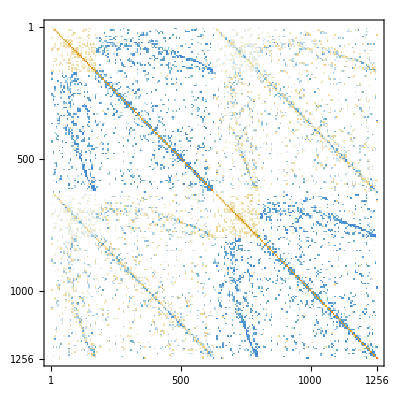
{-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[stiffness],MatrixPlot[minimizedstiffness]}
```

Solving for initial matrix and modified

```mathematica
Short[solution1=LinearSolve[stiffness,load]]
Short[solution2=LinearSolve[minimizedstiffness,load]]
```

{{0.},{0.},{0.},«1250»,{0.},{-0.297192},{-0.310031}}

{{-3.33383×10^-14},«1254»,{-0.2372}}

```mathematica
split=Span@@@Transpose[{Most[#+1],Rest[#]}&[md["IncidentOffsets"]]]
```

{1;;628,629;;1256}

```mathematica
ufun1=ElementMeshInterpolation[{mesh}, solution1[[split[[1]]]]]
vfun1=ElementMeshInterpolation[{mesh}, solution1[[split[[2]]]]]
ufun2=ElementMeshInterpolation[{mesh}, solution2[[split[[1]]]]]
vfun2=ElementMeshInterpolation[{mesh}, solution2[[split[[2]]]]]
```

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

«1 more identical outputs»

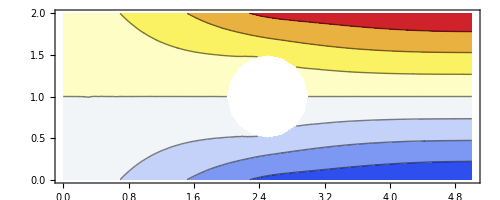
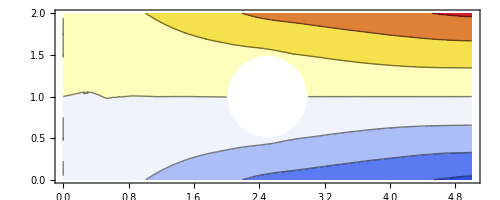

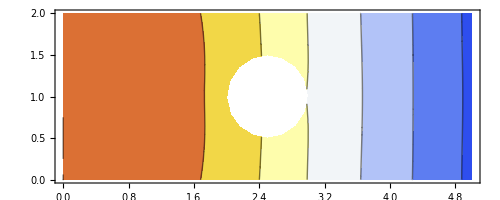
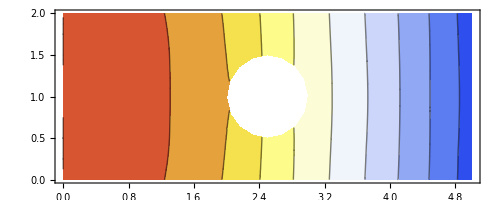

```mathematica
{ContourPlot[ufun1[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic],ContourPlot[ufun2[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]}
{ContourPlot[vfun1[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic],
ContourPlot[vfun2[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]}
```

```mathematica
dmesh1=ElementMeshDeformation[mesh,{ufun1,vfun1}]
dmesh2=ElementMeshDeformation[mesh,{ufun2,vfun2}]
```

ElementMesh[{{0.,5.07859},{-0.310995,2.}},{TriangleElement[<282>]}]

ElementMesh[{{-5.43269×10^-14,5.06319},{-0.239585,2.}},{TriangleElement[<282>]}]

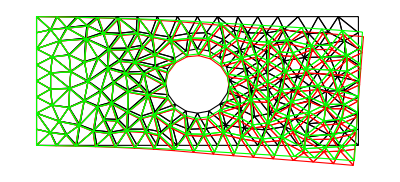

```mathematica
Show[{
mesh["Wireframe"],
dmesh1["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]],
dmesh2["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Green],FaceForm[]]]]
}]
```

Visualization of densities of elements

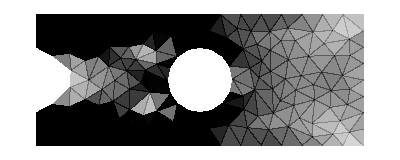

```mathematica
polys=Polygon[#]&/@(
Apply[{coords[[#1]],coords[[#2]],coords[[#3]]}&]/@elems[[1,1,1;;Length[square],1;;3]]);
maxden=Max[minimizedDen];
denpolys=Transpose[{minimizedDen/maxden,polys}];
filteredpolys=Select[denpolys,#[[1]]>0.0&];
opacityfiltered=Replace[#,{x_,y_}:>{Opacity[x],y}]&/@filteredpolys;
Graphics[opacityfiltered]
```